```mathematica
(*Second derivative is long and unwieldly*)
```

```mathematica
D[(1-Exp[-2n(Subscript[g, n]-y)(Subscript[g, n-1]-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,2}]
```

1/(√(2 π))√n ((1-ⅇ^(-2 n (-x+g_(-1+n)) (-y+g_n))) (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)+4 ⅇ^(-1/2 n (-x+y)^2-2 n (-x+g_(-1+n)) (-y+g_n)) n^2 (-x+y) (-x+g_(-1+n))-4 ⅇ^(-1/2 n (-x+y)^2-2 n (-x+g_(-1+n)) (-y+g_n)) n^2 (-x+g_(-1+n))^2)

```mathematica
(*Trying to solve for points of intersection to deal with ∫Abs[f]ⅆx. Appears to not work*)
```

```mathematica
Solve[1/(√(2 π))√n ((1-ⅇ^(-2 n (-x+Subscript[g, -1+n]) (-y+Subscript[g, n]))) (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)+4 ⅇ^(-1/2 n (-x+y)^2-2 n (-x+Subscript[g, -1+n]) (-y+Subscript[g, n])) n^2 (-x+y) (-x+Subscript[g, -1+n])-4 ⅇ^(-1/2 n (-x+y)^2-2 n (-x+Subscript[g, -1+n]) (-y+Subscript[g, n])) n^2 (-x+Subscript[g, -1+n])^2)==0,y]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(√n ((1-ⅇ^(-2 n (-x+g_(-1+n)) (-y+g_n))) (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)+4 ⅇ^(-1/2 n (-x+y)^2-2 n (-x+g_(-1+n)) (-y+g_n)) n^2 (-x+y) (-x+g_(-1+n))-4 ⅇ^(-1/2 n (-x+y)^2-2 n (-x+g_(-1+n)) (-y+g_n)) n^2 (-x+g_(-1+n))^2))/(√(2 π))==0,y]

```mathematica
(*What the function looks like beyond the boundary. We can't appeal to any symmetry arguments here*)
```

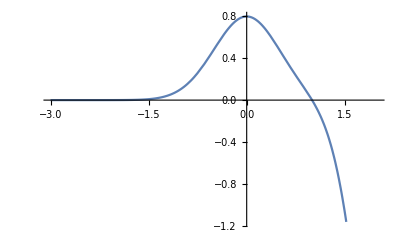

```mathematica
Plot[Evaluate[D[(1-Exp[-2n(Subscript[g, n]-y)(Subscript[g, n-1]-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,0}]/.Subscript[g, n]-> 1/. Subscript[g, n-1]->1.2/.n->4 /.x-> 0],{y,-3,2}]
```

```mathematica
(*Periodized Bernoulli polynomial*)
```

```mathematica
PBernoulliB[n_,x_]:=BernoulliB[n,x - Floor[x]]
```

```mathematica
(*Second Periodized Bernoulli polynomial*)
```

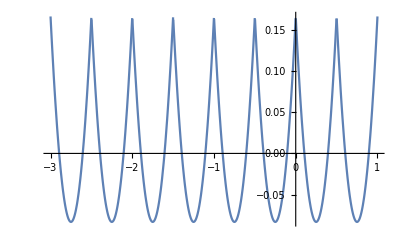

```mathematica
Plot[PBernoulliB[2,-x/0.5],{x,-3,1}]
```

```mathematica
Manipulate[Plot[PBernoulliB[2,-y n],{y,-3,1},PlotRange->{{-3,1},{-2,2}}],{n,4,15,1},{x,-3,1},{g2,0.5,1},{g1,0.5,1}]
```

```mathematica
(*Looking at what the second derivative looks like for different values of x. Function has large negative values, making the absolute value an issue.*)
```

```mathematica
Manipulate[Plot[Evaluate[D[(1-Exp[-2n(g2-y)(g1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,2}] ],{y,-3,g2},PlotRange->{{-3,1},{-15,15}}],{n,4,15,1},{x,-3,g1},{g2,0.5,1},{g1,0.5,1}]
```

```mathematica
Manipulate[Plot[Evaluate[PBernoulliB[2,-y n]*D[(1-Exp[-2n(g2-y)(g1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,2}] ],{y,-3,g2},PlotRange->{{-3,1},{-3,3}}],{n,4,40,2},{x,-3,g1,1/n},{g2,0.5,1},{g1,0.5,1}]
```

```mathematica
(* Evaluating the integral ∫_(-∞)^g P(x)(d^2 f)/dx^2 ⅆx in Subscript[r, p] for different values of n. Seems to be rather stable*)
```

```mathematica
ap=Abs[Table[NIntegrate[Evaluate[PBernoulliB[n,-y n]*D[(1-Exp[-2n(g2-y)(g1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,2}]]/.x-> 0/. g1-> 1/. g2-> 1,{y,-∞,1},WorkingPrecision->100],{n,1,8}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-2.970884102671715654782165154351045377963568376581837659189369237171606465853311418746150066616602031}. NIntegrate obtained -5.622581889601786786236467540809025728233027095984759507305656620119424413243586093580526279693261773×10^-6 and 0.00004672421516881720959109751245670644602642063625030006014973485591709515171904184306547056463431346464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-0.9941557896499404342288012986956903923585217271065576720606545300996538267682694682570766317257497665}. NIntegrate obtained 0.001133496197027393652023336154784289591882976052700932048683153235167549583622364140918710917561947527 and 9.756605274571510925645266178392886502775188716468454847369649391578458271089978060530621410079647098×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-1.32467993949945230900860400525412294497826670488886404648603042195291697481240108383731362280302719}. NIntegrate obtained 7.873133710651489333539772333187960210648808770183941760498305323687096464576072663102159786489848366×10^-12 and 6.351678044655399695639758024536672790705714259250875730719154729524018676385427754338837816402628839×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{5.622581889601786786236467540809025728233027095984759507305656620119424413243586093580526279693261773×10^-6,0.001133496197027393652023336154784289591882976052700932048683153235167549583622364140918710917561947527,7.873133710651489333539772333187960210648808770183941760498305323687096464576072663102159786489848366×10^-12,0.000181335478114975695238417592850091413454306268077377634037052449952814805948699120083091313593862618,2.569557773538743457124317440848658545994418597438520831251158537564745846016744872550039947750471841×10^-16,0.0001759339156984584584208808116864918780456280265481397699855646329047090896933676915605287535490191595,8.057363101844531841456136973641903643331830796515272477644566812248441854272134688168315184311317065×10^-21,0.0001740400038676872932256436612373985351845755141436747694123851850641668234304243496694325468998257517}

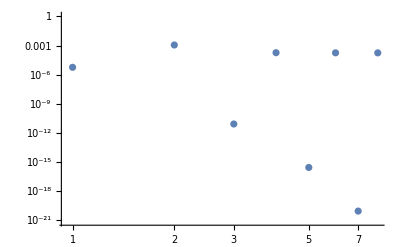

```mathematica
ListLogLogPlot[ap]
```

```mathematica
(* Evaluating the integral ∫_(-∞)^g|(d^2 f)/dx^2|ⅆx in Subscript[r, p] for different values of n. Seems to diverge like O(n). Also seems invariant in x, as expected from the plot of (d^2 f)/dx^2, *)
```

```mathematica
bp=Abs[Table[NIntegrate[Abs[Evaluate[D[(1-Exp[-2n(g2-y)(g1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,2}]]]/.x-> 0.6/. g1-> 1/. g2-> 1,{y,-∞,1},WorkingPrecision->50],{n,1,6}]]
```

NIntegrate::precw: The precision of the argument function (Abs[-0.64\ ⅇ^-0.8\ Plus[« 2 »] - 1/2\ Power[« 2 »] + (1 - ⅇ^Times[« 2 »])\ (-ⅇ^Times[« 2 »] + ⅇ^Times[« 2 »]\ Plus[« 2 »]^2) - 1.6\ ⅇ^-0.8\ Plus[« 2 »] - 1/2\ Power[« 2 »]\ (0.6  - y)]/√2\ π) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-0.76758073770529580394270577254288251449806614811042}. NIntegrate obtained 0.55791916259663395326758439607864029638089096350717 and 3.0732202198953500190953188991494668461526136129887×10^-8 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (Abs[-2.56\ ⅇ^-1.6\ Plus[« 2 »] - Power[« 2 »] + (1 - ⅇ^Times[« 2 »])\ (-2\ ⅇ^Times[« 2 »] + 4\ ⅇ^Times[« 2 »]\ Plus[« 2 »]^2) + 6.4\ ⅇ^-1.6\ Plus[« 2 »] - Power[« 2 »]\ (-0.6 + y)]/√π) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-0.28572326904476822814321344943673840508938434271308}. NIntegrate obtained 1.4596300268846497479682127115662708808388792569642 and 1.039622402492120644842407395112578612054720238793×10^-9 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (√3/2\ π\ Abs[-5.76\ ⅇ^-2.4\ Plus[« 2 »] - 3/2\ Power[« 2 »] + (1 - ⅇ^Times[« 2 »])\ (-3\ ⅇ^Times[« 2 »] + 9\ ⅇ^Times[« 2 »]\ Plus[« 2 »]^2) + 14.4\ ⅇ^-2.4\ Plus[« 2 »] - 3/2\ Power[« 2 »]\ (-0.6 + y)]) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-0.081308261409079599378334145052373668493684584229788}. NIntegrate obtained 2.4841110115251185837335514718915654994580678484165 and 3.3547674135637596794452178596290563684506351250084×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{0.55791916259663395326758439607864029638089096350717,1.4596300268846497479682127115662708808388792569642,2.4841110115251185837335514718915654994580678484165,3.5489339973134805348646362810826328974094608058685,4.6106476854767807622078282107611727840514382343618,5.6448596849597305443743721178609763264707174915482}

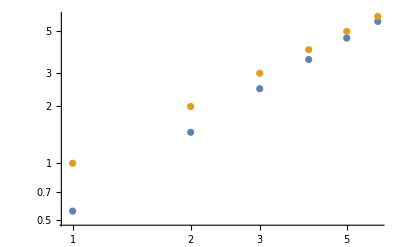

```mathematica
ListLogLogPlot[{bp,Table[n,{n,1,6}]}]
```

```mathematica
(* Looking dominant error term for comparison. As we send n to infinity, the error mass arising from x is concentrated close to g2 and grows like n. But we know that it is unlikely to be near g2, since its very likely you'll have hit the boundary previously. The probability of being near the boundary vanishes like 1/n. This cancellation gives us Ch^2.*)
```

```mathematica
Manipulate[Plot[{2n(g1 -x)PDF[NormalDistribution[0,1/(√n)],x-g2],If[x <g1,1/2 n,0]},{x,-3,g1},PlotRange->Full],{n,1,30,1},{g1,0.5,1},{g2,0.5,1}]
```

```mathematica
(*∫_(-∞)^g P(x)(d^2 f)/dx^2 ⅆx for a fixed n=3*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.736323}. NIntegrate obtained -1.25706×10^-10 and 2.771×10^-16 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

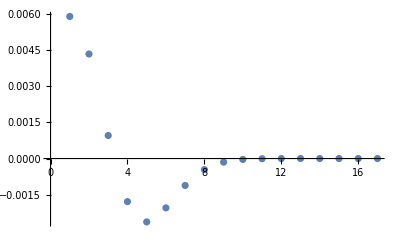

```mathematica
ListPlot[Table[NIntegrate[PBernoulliB[n,-y n]*D[(1-Exp[-2n(1-y)(1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,2}] /. n-> 3,{y,-3,1}],{x,-3,1,0.25}]]
```

```mathematica
(*∫_(-∞)^g P(x)(d^2 f)/dx^2 ⅆx for a fixed n=10*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-2.98496}. NIntegrate obtained -1.59091 and 2.52271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-2.83594}. NIntegrate obtained 0.155803 and 3.40038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-2.98496}. NIntegrate obtained 0.485736 and 1.90716 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

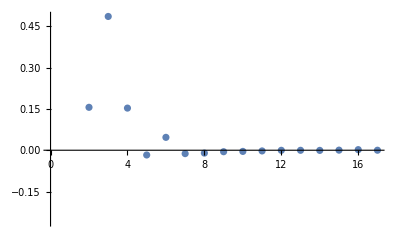

```mathematica
ListPlot[Table[NIntegrate[PBernoulliB[n,-y n]*D[(1-Exp[-2n(1-y)(1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,2}] /. n-> 10,{y,-3,1}],{x,-3,1,0.25}]]
```

```mathematica
(*∫_(-∞)^g |(d^2 f)/dx^2|ⅆx for a fixed n=3. Error appears to be like n for all x. *)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

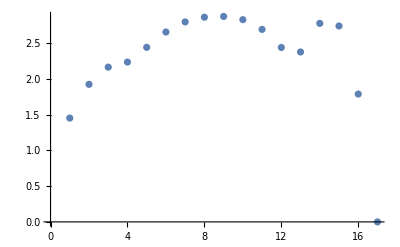

```mathematica
ListPlot[Table[NIntegrate[Abs[D[(1-Exp[-2n(1-y)(1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,2}] ]/. n-> 3,{y,-3,1}],{x,-3,1,0.25}]]
```

```mathematica
(*∫_(-∞)^g |(d^2 f)/dx^2|ⅆx for a fixed n=10. Error appears to be like n for all x. *)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-2.17975}. NIntegrate obtained 7.8716 and 0.0000227412 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-1.67975}. NIntegrate obtained 9.59382 and 0.0000545781 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

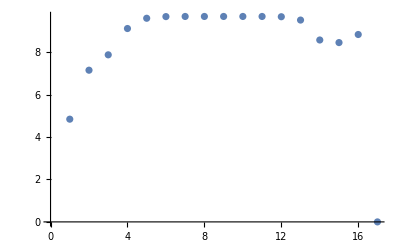

```mathematica
ListPlot[Table[NIntegrate[Abs[D[(1-Exp[-2n(1-y)(1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,2}] ]/. n-> 10,{y,-3,1}],{x,-3,1,0.25}]]
```

```mathematica
Manipulate[Plot[{Evaluate[NIntegrate[Abs[D[(1-Exp[-2n(1-y)(1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,3}] ],{y,-3,1}]],If[x <1,1/2 n,0]},{y,-3,1},PlotRange->Full],{n,1,30,1}]
```